Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

3 - 10 Maclaurin Series
Find the Maclaurin series and its radius of convergence.

3.  Sin[2 z^2]

```mathematica
Clear["Global`*"]
```

By asking for the series to be generated around the origin, I ask for the Maclaurin series,

```mathematica
ser=Series[Sin[2 z^2],{z,0,16}]
```

2 z^2-(4 z^6)/3+(4 z^10)/15-(8 z^14)/315+O[z]^17

It seems that Mathematica cannot provide useful cooperation in the case of the problem function. SumConvergence, with or without TrigReduce, does not seem to work in establishing the radius of convergence. In fact, observe the following,

```mathematica
SumConvergence[Sin[2 z^2],z]
```

False

The false indication makes me wary altogether. So this alternative method. First I will copy from numbered line (14) on p. 695, the series expression of the sine function,

```mathematica
thi=HoldForm[Sum[(-1)^n z^(2 n+1)/((2 n+1)!),{n,0,∞}]]
```

∑_(n=0)^∞ ((-1)^n z^(2 n+1))/((2 n+1)!)

Mathematica identifies this with sine function immediately, thus the need for HoldForm to prevent undesired simplification. Then to modify the sine series to match the problem expression,

```mathematica
thi2=thi/.z->2 z^2
```

∑_(n=0)^∞ ((-1)^n (2 z^2)^(2 n+1))/((2 n+1)!)

Now I will hand this term on to the SumConvergence function,

```mathematica
SumConvergence[((-1)^n (2 z^2)^(2 n+1))/((2 n+1)!),n]
```

True

The previous cell confirms convergence, but I want the radius of convergence. To use the Cauchy-Hadamard formula, I need to separate the z and n parts of the expression,

```mathematica
Expand[(2 z^2)^(2 n+1)]
```

2^(1+2 n) (z^2)^(1+2 n)

The above form reveals the center of the series, which is 0, no great surprise for a Maclaurin series. Note that z, when called on, will be raised to the 4th power of n. Okay, at this point I can use the Cauchy-Hadamard formula,

```mathematica
Limit[Abs[((-1)^n 2^(1+2 n))/((2 n+1)!)(((2 n+2)!)/((-1)^(n+1) 2^(2+2 n)))],n->∞]
```

∞

Applying the power of the power term,

```mathematica
∞^(1/4)
```

∞

The above answer matches the radius of convergence shown in the text’s answer.

5.  1/(2+z^4)

```mathematica
Clear["Global`*"]
```

By asking for the series to be generated around the origin, I ask for the Maclaurin series,

```mathematica
Series[1/(2+z^4),{z,0,16}]
```

1/2-z^4/4+z^8/8-z^12/16+z^16/32+O[z]^17

Testing for convergence,

```mathematica
SumConvergence[1/(2+z^4),z]
```

True

in a verification of some radius of convergence. Then try to find the radius of convergence the easy way,

```mathematica
Sum[1/(2+z^4),{z,0,∞},GenerateConditions->True]
```

1/8 (2+(-2)^(1/4) π Cot[(-2)^(1/4) π]+(-2)^(1/4) π Coth[(-2)^(1/4) π])

The above cell is beyond my capability to simplify, and Mathematica won’t alter it either. I can kludge the general term,

```mathematica
tri[n_]=(-1)^n z^(4 n)/2^(n+1)
```

(-1)^n 2^(-1-n) z^(4 n)

and check it,

```mathematica
TableForm[Table[{n,tri[n]},{n,0,4}]]
```

0 | 1/2
1 | -z^4/4
2 | z^8/8
3 | -z^12/16
4 | z^16/32

At this point it looks like I’m ready to try Cauchy-Hadamard,

```mathematica
Limit[Abs[(-1)^n/2^(n+1)(2^(n+2)/(-1)^(n+1))],n->∞]
```

2

And the power of the power term is 4, thus

```mathematica
(2)^(1/4)
```

2^(1/4)

The above cell matches the answer in the text.

7.  Cos[z/2]^2

```mathematica
Clear["Global`*"]
```

Calling for my Maclaurin,

```mathematica
Series[Cos[z/2]^2,{z,0,12}]
```

1-z^2/4+z^4/48-z^6/1440+z^8/80640-z^10/7257600+z^12/958003200+O[z]^13

Somehow I need to put together the general term,

```mathematica
FindSequenceFunction[{-4,48,-1440,80640,-7257600,958003200},n]
```

(-1)^n 2^(1+2 n) Pochhammer[1/2,n] Pochhammer[1,n]

I couldn’t get an answer out of Mathematica using the above function unless I dropped the first term of the series. Trying to simplify a bit,

```mathematica
FullSimplify[%]
```

2 (-1)^n Gamma[1+2 n]

The Gamma function is not difficult, although some of the others Mathematica throws out are daunting. In general in this situation though, the amount of knowledge necessary consists solely of knowing how to form the a_(n+1) term from the a_n term.

```mathematica
testg[n_]=(-1)^n 2 Gamma[1+2n]
```

2 (-1)^n Gamma[1+2 n]

```mathematica
testh[n_]=(-1)^n 2 (2 n)!
```

2 (-1)^n (2 n)!

Checking, starting with n=1,

```mathematica
TableForm[Table[{n,testg[n],testh[n]},{n,1,6}]]
```

1 | -4 | -4
2 | 48 | 48
3 | -1440 | -1440
4 | 80640 | 80640
5 | -7257600 | -7257600
6 | 958003200 | 958003200

testh[n] was lifted from the text answer. If I had had a brainwave and had seen the pattern on my own, the process would be more direct than using FindSequenceFunction.

Setting up the n part of the expression, not worrying about the z part at the moment,

```mathematica
coef=(-1)^n/(2 Gamma[1+2 n])
```

(-1)^n/(2 Gamma[1+2 n])

Ready to examine the limit governing the Cauchy-Hadamard. Not having the initial term should not be a handicap, as I have my sights set on much bigger terms now,

```mathematica
Limit[Abs[(-1)^n/(2 Gamma[1+2 n])((2 Gamma[1+2 (n+1)])/(-1)^(n+1))],n->∞]
```

∞

Up until now I have ignored the power term. But it is of the form z^(2 n). So applying its effect amounts to

```mathematica
∞^(1/2)
```

∞

The green cell above matches the answer in the text. (That a_0 term that I ignored, I continue to treat as inconsequential.)

9.  Integrate[Exp[-t^2/2],{t,0,z}]

```mathematica
Clear["Global`*"]
```

Calling for my Maclaurin,

```mathematica
Series[Exp[-t^2/2],{t,0,12}]
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080+O[t]^13

At https : // www.dummies.com/education/math/calculus/how - to - integrate - a - power - series/ I learned how to integrate a power series term by term. A key concept was that after the term by term integration you can turn the result back into another power series. So how about a short cut, would that work?

```mathematica
Integrate[Exp[-t^2/2],{t,0,z}]
```

√(π/2) Erf[z/(√2)]

```mathematica
Series[√(π/2) Erf[z/(√2)],{z,0,15}]
```

z-z^3/6+z^5/40-z^7/336+z^9/3456-z^11/42240+z^13/599040-z^15/9676800+O[z]^16

The above green cell matches the text answer. The thing I haven’t got yet is the radius of convergence.

Aiming to build the general term,

```mathematica
FindSequenceFunction[{1,-6,40,-336,3456,-42240,599040,-9676800},n]
```

(-1)^(1+n) 2^(-1+n) (-1+2 n) Pochhammer[1,-1+n]

```mathematica
FullSimplify[%]
```

(-1)^(1+n) 2^(-1+n) (-1+2 n) Gamma[n]

```mathematica
testg[n_]=(-1)^(1+n)2^(-1+n) (-1+2 n) Gamma[n]
```

(-1)^(1+n) 2^(-1+n) (-1+2 n) Gamma[n]

```mathematica
testh[n_]=(-1)^(1+n)(2n-1) 2^(n-1)(n-1)!
```

(-1)^(1+n) 2^(-1+n) (-1+2 n) (-1+n)!

```mathematica
TableForm[Table[{n,testg[n],testh[n]},{n,1,7}]]
```

1 | 1 | 1
2 | -6 | -6
3 | 40 | 40
4 | -336 | -336
5 | 3456 | 3456
6 | -42240 | -42240
7 | 599040 | 599040

testh[n], inspired from the text answer, and realized through the FindSeqenceFunction, begs the search, because I could not have done it entirely on my own.

Setting up the n part of the expression, not worrying about the z part at the moment,

```mathematica
coef=(-1)^(n+1)/(2^(-1+n) (-1+2 n) Gamma[n])
```

((-1)^(1+n) 2^(1-n))/((-1+2 n) Gamma[n])

Ready to examine the limit governing the Cauchy-Hadamard.

```mathematica
Limit[Abs[(-1)^(n+1)/(2^(-1+n) (-1+2 n) Gamma[n])((2^n (-1+2 (n+1)) Gamma[n+1])/(-1)^(n+2))],n->∞]
```

∞

Up until now I have ignored the power term. But it is of the form z^(2 n-1). So applying its effect amounts to going with my old standard policy of regarding only the part of the term involving n, which makes it, in this case, 2 n. So,

```mathematica
∞^(1/2)
```

∞

The green cell above matches the answer in the text.

11 - 14 Higher transcendental functions
Find the Maclaurin series by termwise integrating the integrand. (The integrals cannot be evaluated by the usual methods of calculus. They define the error function erf z, sine integral Si(z) and Fresnel integrals S(z) and C(z), which occur in statistics, heat conduction, optics, and other applications. These are special so-called higher transcendental functions.)

11.  S[z_]=Integrate[Sin[t^2],{t,0,z}]

```mathematica
Clear["Global`*"]
```

Getting ready to work on a Fresnel integral. Working this experimentally. First, I use plain old Integrate applied to the problem function,

```mathematica
Integrate[Sin[t^2],{t,0,z}]
```

√(π/2) FresnelS[√(2/π) z]

As the above cell shows, the answer to the integration is expressed in FresnelS, a function which is built in to Mathematica. So I can express this answer as a series, saving aside the leading coefficient for now,

```mathematica
Series[FresnelS[√(2/π) z],{z,0,36}]
```

1/3 √(2/π) z^3-z^7/(21 (√2 √π))+z^11/(660 √2 √π)-z^15/(37800 (√2 √π))+z^19/(3447360 √2 √π)-z^23/(459043200 (√2 √π))+z^27/(84064780800 √2 √π)-z^31/(20268952704000 (√2 √π))+z^35/(6224529991680000 √2 √π)+O[z]^37

Then, inserting the coefficient and simplifying, I get

```mathematica
Simplify[√(π/2)(1/3 √(2/π) z^3-z^7/(21 (√2 √π))+z^11/(660 √2 √π)-z^15/(37800 (√2 √π))+z^19/(3447360 √2 √π)-z^23/(459043200 (√2 √π))+z^27/(84064780800 √2 √π)-z^31/(20268952704000 (√2 √π))+z^35/(6224529991680000 √2 √π)+O[z]^37)]
```

z^3/3-z^7/42+z^11/1320-z^15/75600+z^19/6894720-z^23/918086400+z^27/168129561600-z^31/40537905408000+z^35/12449059983360000+O[z]^37

And the above green cell happens to be the answer. There is still the radius of convergence to discover. It takes a little work to get the FindSequenceFunction enough numbers to consider, here, 8, in order to yield an answer. It wouldn’t do it with 7. When it did return an answer, it was nearly instantaneous, in spite of the rather large numbers involved.

```mathematica
FindSequenceFunction[{3,-42,1320,-75600,6894720,-918086400,168129561600,-40537905408000},n]
```

(-1)^(1+n) 4^(-1+n) (-1+4 n) Pochhammer[1,-1+n] Pochhammer[3/2,-1+n]

```mathematica
FullSimplify[%]
```

(-1)^(1+n) (-1+4 n) Gamma[2 n]

Now, like before, I’ll test to make sure the denominator coefficients spawn true.

```mathematica
testg[n_]=(-1)^(1+n) (-1+4 n) Gamma[2 n]
```

(-1)^(1+n) (-1+4 n) Gamma[2 n]

```mathematica
testh[n_]=(-1)^(1+n)(2 n-1)!(4 n-1)
```

(-1)^(1+n) (-1+4 n) (-1+2 n)!

```mathematica
TableForm[Table[{n,testg[n],testh[n]},{n,1,7}]]
```

1 | 3 | 3
2 | -42 | -42
3 | 1320 | 1320
4 | -75600 | -75600
5 | 6894720 | 6894720
6 | -918086400 | -918086400
7 | 168129561600 | 168129561600

testh[n] was lifted from the text answer. If I had had magic synapses and had seen the pattern on my own, the process might have been slightly simpler than using FindSequenceFunction.

Setting up the n part of the Cauchy-Hadamard expression, not worrying about the z part at the moment,

```mathematica
coef=(-1)^(1+n)(-1+4 n) Gamma[2 n]
```

(-1)^(1+n) (-1+4 n) Gamma[2 n]

```mathematica
Limit[Abs[1/((-1)^(1+n)(-1+4 n) Gamma[2 n])(((-1)^(2+n)(-1+4( n+1)) Gamma[2( n+1)])/1)],n->∞]
```

∞

How about the power term? The power of the power term is 2n+1. Which from my method in previous problems, will have the effect of

```mathematica
∞^(1/2)
```

∞

13.  erf[z]=2/(√π)Integrate[ⅇ^(-t^2),{t,0,z}]

```mathematica
Clear["Global`*"]
```

To match the text answer, it will help to set aside the leading coefficient for a moment,

```mathematica
Integrate[ⅇ^(-t^2),{t,0,z}]
```

1/2 √π Erf[z]

Mathematica immediately rolls it up into the eponymus function.

```mathematica
Series[1/2 √π Erf[z],{z,0,12}]
```

z-z^3/3+z^5/10-z^7/42+z^9/216-z^11/1320+O[z]^13

Then restoring the coefficient,

```mathematica
2/(√π)(z-z^3/3+z^5/10-z^7/42+z^9/216-z^11/1320+O[z]^13)
```

gives me the text answer.

18 - 25 Taylor series
Find the Taylor series with center z_0 and its radius of convergence.

19.  1/(1-z), z_0=1

```mathematica
Clear["Global`*"]
```

First, a naïve try,

```mathematica
ard=Series[1/(1-z),{z,1,8}]
```

-1/(z-1)+O[z-1]^9

is not successful. The s.m. advises to work this according to example 7, p. 696, using c=1 and z_0=ⅈ, developing in powers of z-z_0, where c-z_0 ≠0. It would look like

```mathematica
1/(c-z)==1/(1-z)==1/(1-Subscript[z, 0]-(z-Subscript[z, 0]))==1/(1-ⅈ-(z-ⅈ))==1/((1-ⅈ)(1-(z-ⅈ)/(1-ⅈ)))==1/(1-ⅈ)∑_(n=0)^∞ ((z-ⅈ)/(1-ⅈ))^n;
```

working from the analogous progression of terms in the example. To get across the last double-equals sign involves numbered lines (7), (7*), (8*), and (8) on p. 691.

Taking the expression to the right of the last double-equals sign, and multiplying by (1+ⅈ)/(1+ⅈ) both inside and outside the sigma, gives

```mathematica
(1+ⅈ)/2∑_(n=0)^∞ ((1+ⅈ)/2)^n(z-ⅈ)^n
```

as the general term. Putting it in a form that can be easily compared with the text answer, and asking for 7 terms instead of an infinite number,

```mathematica
Sum[(1+ⅈ)/2 Sequence[((1+ⅈ)/2)^n(z-ⅈ)^n],{n,0,6}]
```

(1/2+ⅈ/2)+1/2 ⅈ (-ⅈ+z)-(1/4-ⅈ/4) (-ⅈ+z)^2-1/4 (-ⅈ+z)^3-(1/8+ⅈ/8) (-ⅈ+z)^4-1/8 ⅈ (-ⅈ+z)^5+(1/16-ⅈ/16) (-ⅈ+z)^6

The green cell above matches the answer in the text, for series form. As for the radius of convergence, also using example 7,

```mathematica
Reduce[Abs[(z-ⅈ)/(1-ⅈ)]<1,z]
```

-√2<Re[z]<√2&&1-(√(4-2 Re[z]^2))/(√2)<Im[z]<1+(√(4-2 Re[z]^2))/(√2)

The real part of the yellow cell matches the text answer, but the text answer is silent as to imaginary parts.

If the yellow cell is correct, a plot of the radius of curvature would resemble the one below,

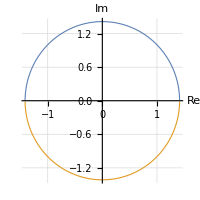

```mathematica
ParametricPlot[{{z,(√(4-2 z^2))/(√2)},{z,-(√(4-2 z^2))/(√2)}},{z,-√2,√2},ImageSize->200,AxesLabel->{"Re","Im"},PlotRange->All,AspectRatio->Automatic,GridLines->Automatic,PlotStyle->{Thickness[0.004]}]
```

21.  Sin[z], z_0=π/2

```mathematica
Clear["Global`*"]
```

First, a naïve try,

```mathematica
Series[Sin[z],{z,π/2,12}]
```

1-1/2 (z-π/2)^2+1/24 (z-π/2)^4-1/720 (z-π/2)^6+(z-π/2)^8/40320-(z-π/2)^10/3628800+(z-π/2)^12/479001600+O[z-π/2]^13

Surprisingly, this one pops right out. Using the powers of the power terms, I think I can actually deduce the sequence of this one. On second thought, maybe I will use FindSequenceFunction, since it is so much easier,

```mathematica
FindSequenceFunction[{1,-2,24,-720,40320,-3628800,479001600},n]
```

(-1)^(1+n) 4^(-1+n) Pochhammer[1/2,-1+n] Pochhammer[1,-1+n]

```mathematica
FullSimplify[%]
```

(-1)^(1+n) Gamma[-1+2 n]

```mathematica
testg[n_]=(-1)^(1+n) Gamma[-1+2 n]
```

(-1)^(1+n) Gamma[-1+2 n]

```mathematica
TableForm[Table[{n,testg[n]},{n,1,7}]]
```

1 | 1
2 | -2
3 | 24
4 | -720
5 | 40320
6 | -3628800
7 | 479001600

Setting up the n part of the Cauchy-Hadamard expression, not worrying about the z part at the moment,

```mathematica
Limit[Abs[1/((-1)^(1+n) Gamma[-1+2 n])(((-1)^(2+n) Gamma[-1+2( n+1)])/1)],n->∞]
```

∞

How about the power term? In this problem, the power term is determined in a simple way. (It’s surprising how addictive that FSF can become.)

```mathematica
FindSequenceFunction[{0,2,4,6,8,10,12},n]
```

2 (-1+n)

And having the effect of

```mathematica
∞^(1/2)
```

∞

Which agrees with the text answer.

23.  1/(z+ⅈ)^2, z_0=ⅈ

```mathematica
Clear["Global`*"]
```

First, a naïve try,

```mathematica
Series[1/(z+ⅈ)^2,{z,ⅈ,8}]
```

-1/4-1/4 ⅈ (z-ⅈ)+3/16 (z-ⅈ)^2+1/8 ⅈ (z-ⅈ)^3-5/64 (z-ⅈ)^4-3/64 ⅈ (z-ⅈ)^5+7/256 (z-ⅈ)^6+1/64 ⅈ (z-ⅈ)^7-(9 (z-ⅈ)^8)/1024+O[z-ⅈ]^9

The green cell above matches the text answer. Now to address a strange looking sequence of term coefficients

```mathematica
FindSequenceFunction[{-1/4,-ⅈ/4,3/16,ⅈ/8,-5/64,-(3ⅈ)/64,7/256,ⅈ/64,-9/1024},n]
```

(ⅈ/2)^(1+n) n

```mathematica
testg[n_]=(ⅈ/2)^(1+n) n
```

(ⅈ/2)^(1+n) n

```mathematica
TableForm[Table[{n,testg[n]},{n,1,9}]]
```

1 | -1/4
2 | -ⅈ/4
3 | 3/16
4 | ⅈ/8
5 | -5/64
6 | -(3 ⅈ)/64
7 | 7/256
8 | ⅈ/64
9 | -9/1024

Setting up the n part of the Cauchy - Hadamard expression, not worrying about the z part at the moment. Since I looked for the complete coefficient this time, not just the denominator part, the relation of n and n+1 parts is different,

```mathematica
Limit[Abs[((ⅈ/2)^(1+n) n)/1(1/((ⅈ/2)^(2+n)(n+1)))],n->∞]
```

2

In this problem the power of the power term is simply n. Since I haven’t been concerned about the presence of a non-n factor in the power term up to now, I won’t let myself be bothered if it happens to be imaginary. So I give the final radius as

```mathematica
2^(1/1)
```

2

The green cell agrees with the text answer.

25.  Sinh[2 z-ⅈ], z_0=ⅈ/2

```mathematica
Clear["Global`*"]
```

First, a naïve try,

```mathematica
Series[Sinh[2 z-ⅈ],{z,ⅈ/2,15}]
```

2 (z-ⅈ/2)+4/3 (z-ⅈ/2)^3+4/15 (z-ⅈ/2)^5+8/315 (z-ⅈ/2)^7+(4 (z-ⅈ/2)^9)/2835+(8 (z-ⅈ/2)^11)/155925+(8 (z-ⅈ/2)^13)/6081075+(16 (z-ⅈ/2)^15)/638512875+O[z-ⅈ/2]^16

The green cell above matches the text answer. Now to try to indentify the term coefficients

```mathematica
FindSequenceFunction[{2,4/3,4/15,8/315,4/2835,8/155925,8/6081075},n]
```

2/(Pochhammer[1,-1+n] Pochhammer[3/2,-1+n])

```mathematica
FullSimplify[%]
```

2^(-1+2 n)/Gamma[2 n]

```mathematica
testg[n_]=2^(-1+2 n)/Gamma[2 n]
```

2^(-1+2 n)/Gamma[2 n]

```mathematica
TableForm[Table[{n,testg[n]},{n,1,9}]]
```

1 | 2
2 | 4/3
3 | 4/15
4 | 8/315
5 | 4/2835
6 | 8/155925
7 | 8/6081075
8 | 16/638512875
9 | 4/10854718875

Setting up the n part of the Cauchy - Hadamard expression, not worrying about the z part yet. Looking a lot like the last problem at the moment.

```mathematica
Limit[Abs[2^(-1+2 n)/Gamma[2 n](Gamma[2 (n+1)]/2^(-1+2( n+1)))],n->∞]
```

∞

Now to handle the power term part of the radius calculation. The power of the power term is 2n-1. So the effect of the power term will be

```mathematica
∞^(1/2)
```

∞

The green cell matches the text answer.